```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_confirmed_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsRecovered = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_recovered_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsDeaths = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_deaths_global.csv",CharacterEncoding->"UTF8"],1];
CountryListOri=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[2]]]];
(*Export[NotebookDirectory[]<>"/countries.xls",TableForm[Table[{i,CountryListOri[[i]][[2]]},{i,1,Length[CountryList]}]],"XLS"];*)

(* Add population data and ISO code to the countrylist *)
ISOCountries =Drop[Import[NotebookDirectory[]<>"/ISO-countries.csv", CharacterEncoding->"UTF8"],1];
CountryList={};
For[i=1,i≤Length[CountryListOri],i++,
notfound=1;
For[j=1,j≤Length[ISOCountries],j++,
If[CountryListOri[[i]]==ISOCountries[[j]][[2]],notfound=0;CountryList=Append[CountryList,ISOCountries[[j]]]]
]
If[notfound==1,Print["Not found: "<>CountryListOri[[i]]]];
]
```

Not found: Diamond Princess

Not found: Kosovo

Not found: MS Zaandam

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByCountry = Table[{},{i,1,Length[CountryList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-4;

For[country = 1, country ≤ Length[CountryList],country++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempRecovered = Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[CountryList[[country]][[2]], HopkinsConfirmed[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsRecovered],row++,
If[StringMatchQ[CountryList[[country]][[2]], HopkinsRecovered[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempRecovered= TempRecovered + Drop[HopkinsRecovered[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[CountryList[[country]][[2]], HopkinsDeaths[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],4];
]
];
TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempRecoveredDiff=TempRecovered-Drop[Join[{0},TempRecovered],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByCountry[[country]]= {ToString[CountryList[[country]][[2]]],TempConfirmed,TempRecovered,TempDeaths,TempConfirmedDiff,TempRecoveredDiff,TempDeathsDiff};
]
```

```mathematica
(* Model *)
SIR[country_,dday_] := (
n=n0;
e=e0;
i=i0;
r=0;
m=0;
c=r+r+m;
s = n-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = (gamma+delta) * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
de=lambda i * (s/n)-epsilon e;
di = epsilon e -gamma i - delta i;
inew = lambda i * (s/n);
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
e+=de;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+e+i+r;
risk=i*listr0[[sirday]][[2]];
If[sirday≤ Length[DataByCountry[[country]][[2]]],
cost = cost + (c-DataByCountry[[country]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di,dm,inew,risk}];
);
```

```mathematica
(* Initial values for this country *)
Window =4;(* Number of days over which to fit the model *)
future=30; (* Number of days to project ahead *)
```

```mathematica
CountrySIR[country_] := (
CurrentCountry =country;
today = Length[DataByCountry[[CurrentCountry]][[2]]];
CFR=DataByCountry[[CurrentCountry]][[4]][[-1]]/DataByCountry[[CurrentCountry]][[2]][[-1]];

n0 = CountryList[[country]][[3]];
e0=5;
i0=1;
epsilon = 1/2;
gamma=(1-CFR)/12.4;
delta = CFR/10.4;
listr0 = {};
For[day = 1, day <= Length[DataByCountry[[CurrentCountry]][[2]]] + future, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];

(* Fit model to the data *)
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[CurrentCountry,day+Window][[6]];
For[kr0 = 0.1,kr0≤20,kr0=kr0+4.05,
(* set this possible r0 for all following days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[CurrentCountry,day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];

(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];

(* Generate the lists of data for the plots *)
lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
listdm={};
listinew = {};
listrisk={};
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]+future,day++,
temp=SIR[CurrentCountry,day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
listdm=Append[listdm,{day,temp[[8]]}];
listinew = Append[listinew,{day,temp[[9]]}];
listrisk = Append[listrisk,{day,temp[[10]]}];
];
Return[{CurrentCountry,DataByCountry[[CurrentCountry]][[1]],listr0,listi,listr,listm,listc,listdi,listdm,listinew,listrisk}];
);
```

```mathematica
CountrySIR[17];
```

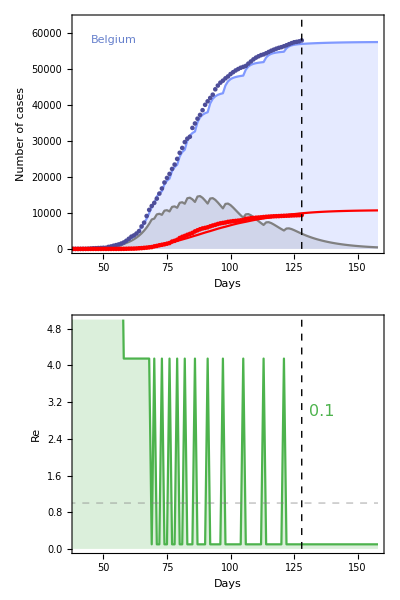

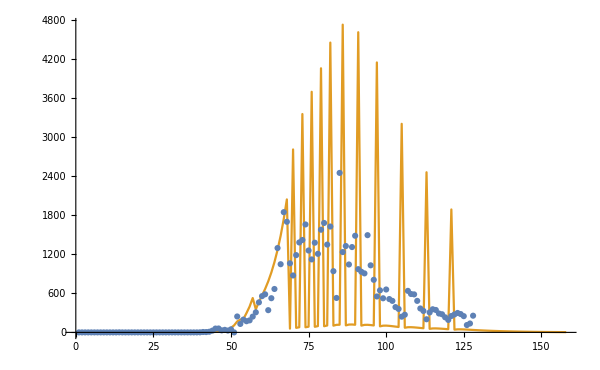

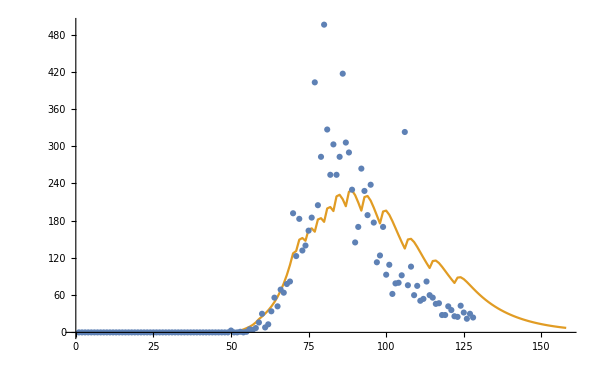

```mathematica
(* Generate plots *)
height=Max[ {Max[Drop[listc,-55]],Max[DataByCountry[[CurrentCountry]][[2]]]}];

If[listr0[[-1]][[2]]<0.8,R0Color=RGBColor[0.3,0.7,0.3],If[listr0[[-1]][[2]]>1.2,R0Color=RGBColor[0.7,0.3,0.3],R0Color=RGBColor[0.9,0.7,0.3]]];

plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], FontSize->16,R0Color],{today+3,3},{Left,Center}]}];

plotLine = Graphics[Style[Line[{{0, 1}, {today+future, 1}}],Dashed,RGBColor [0.5,0.5,0.5,0.5]]];

plotCountryname = Graphics[{Text[Style[DataByCountry[[CurrentCountry]][[1]], Large,RGBColor[0.4,0.5,0.8]],{45,1.00height},{Left,Center}]}];

plotModel=Show[{ListPlot[{listi,listc,DataByCountry[[CurrentCountry]][[2]],DataByCountry[[CurrentCountry]][[4]],listm},PlotRange->{{40,today+future},{0,1.10height}},Joined->{True,True,False,False,True},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.5,0.6,1],RGBColor[0.3,0.3,0.6],Red,Red},FrameLabel->{"Days","Number of cases"},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600],plotCountryname}];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->R0Color,FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/4,PlotRange->{{40,today+future},{0,5}},ImageSize->600];

ThePlotThickens=Multicolumn[{Show[{plotModel,Graphics[{Dashed, Line[{{today, 0}, {today, 1.2 height}}]}]},ImagePadding->{{70,10},{20,10}}],Show[{plotR0,plotFinalR0,plotLine,Graphics[{Dashed, Line[{{today, 0}, {today, 20}}]}]},ImagePadding->{{70,10},{40,5}}]},1]
CountryFilename=NotebookDirectory[]<>"/results/SIR-" <> ToString[DataByCountry[[CurrentCountry]][[1]]] <> "-" <> DateString[{"ISODate"}] <> ".pdf";
Export[CountryFilename, ThePlotThickens, ImageResolution -> 600];
ListPlot[{DataByCountry[[17]][[5]],listinew},Joined->{False,True},PlotRange->All,ImageSize->600]
ListPlot[{DataByCountry[[17]][[7]],listdm},Joined->{False,True},PlotRange->All,ImageSize->600]
```

```mathematica
ResultsPerCountry={};
For[country=1,country≤Length[CountryList],country++,

CFRTemp = {};
For[delay=1,delay≤20,delay++,CFRTemp=Append[CFRTemp,Join[Drop[DataByCountry[[country]][[4]],delay],Table[0,{i,1,delay}]]/DataByCountry[[country]][[2]]]];
meanTemp=Table[CFRTemp[[i]][[SparseArray[CFRTemp[[i]]]["NonzeroPositions"][[-1]][[1]]]],{i,1,20}];
ResultsPerCountry = Append[ResultsPerCountry,Join[CountrySIR[country],{N[Mean[meanTemp]],N[MeanDeviation[meanTemp]]}]];
Print["Country: "<>ResultsPerCountry[[-1]][[2]]<>" -> "<>ToString[ResultsPerCountry[[-1]][[3]][[-1]][[2]]]];
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Country: Afghanistan -> 4.15

Country: Albania -> 0.1

Country: Algeria -> 0.1

Country: Andorra -> 0.1

Country: Angola -> 0.1

Country: Antigua and Barbuda -> 0.1

Country: Argentina -> 0.1

Country: Armenia -> 0.1

Country: Australia -> 0.1

Country: Austria -> 4.15

Country: Azerbaijan -> 0.1

Country: Bahamas -> 0.1

Country: Bahrain -> 4.15

Country: Bangladesh -> 0.1

Country: Barbados -> 0.1

Country: Belarus -> 0.1

Country: Belgium -> 0.1

Country: Belize -> 0.1

Country: Benin -> 0.1

Country: Bhutan -> 4.15

Country: Bolivia -> 4.15

Country: Bosnia and Herzegovina -> 0.1

Country: Botswana -> 0.1

Country: Brazil -> 4.15

Country: Brunei -> 0.1

Country: Bulgaria -> 0.1

Country: Burkina Faso -> 0.1

Country: Burma -> 0.1

Country: Burundi -> 0.1

Country: Cabo Verde -> 0.1

Country: Cambodia -> 0.1

Country: Cameroon -> 0.1

Country: Canada -> 0.1

Country: Central African Republic -> 4.15

Country: Chad -> 0.1

Country: Chile -> 0.1

Country: China -> 0.1

Country: Colombia -> 4.15

Country: Comoros -> 4.15

Country: Congo (Brazzaville) -> 0.1

Country: Congo (Kinshasa) -> 0.1

Country: Costa Rica -> 4.15

Country: Cote d'Ivoire -> 0.1

Country: Croatia -> 0.1

Country: Cuba -> 0.1

Country: Cyprus -> 0.1

Country: Czechia -> 0.1

Country: Denmark -> 0.1

Country: Djibouti -> 4.15

Country: Dominica -> 0.1

Country: Dominican Republic -> 0.1

Country: Ecuador -> 4.15

Country: Egypt -> 0.1

Country: El Salvador -> 0.1

Country: Equatorial Guinea -> 0.1

Country: Eritrea -> 0.1

Country: Estonia -> 0.1

Country: Eswatini -> 0.1

Country: Ethiopia -> 4.15

Country: Fiji -> 0.1

Country: Finland -> 4.15

Country: France -> 0.1

Country: Gabon -> 4.15

Country: Gambia -> 0.1

Country: Georgia -> 0.1

Country: Germany -> 0.1

Country: Ghana -> 4.15

Country: Greece -> 0.1

Country: Grenada -> 0.1

Country: Guatemala -> 4.15

Country: Guinea -> 4.15

Country: Guinea-Bissau -> 4.15

Country: Guyana -> 0.1

Country: Haiti -> 4.15

Country: Holy See -> 0.1

Country: Honduras -> 0.1

Country: Hungary -> 0.1

Country: Iceland -> 0.1

Country: India -> 4.15

Country: Indonesia -> 0.1

Country: Iran -> 0.1

Country: Iraq -> 0.1

Country: Ireland -> 0.1

Country: Israel -> 0.1

Country: Italy -> 0.1

Country: Jamaica -> 0.1

Country: Japan -> 0.1

Country: Jordan -> 0.1

Country: Kazakhstan -> 0.1

Country: Kenya -> 4.15

Country: Korea, South -> 0.1

Country: Kuwait -> 0.1

Country: Kyrgyzstan -> 0.1

Country: Laos -> 0.1

Country: Latvia -> 0.1

Country: Lebanon -> 0.1

Country: Lesotho -> 0.1

Country: Liberia -> 0.1

Country: Libya -> 8.2

Country: Liechtenstein -> 0.1

Country: Lithuania -> 0.1

Country: Luxembourg -> 0.1

Country: Madagascar -> 0.1

Country: Malawi -> 8.2

Country: Malaysia -> 0.1

Country: Maldives -> 0.1

Country: Mali -> 4.15

Country: Malta -> 0.1

Country: Mauritania -> 4.15

Country: Mauritius -> 0.1

Country: Mexico -> 0.1

Country: Moldova -> 4.15

Country: Monaco -> 0.1

Country: Mongolia -> 0.1

Country: Montenegro -> 0.1

Country: Morocco -> 0.1

Country: Mozambique -> 4.15

Country: Namibia -> 4.15

Country: Nepal -> 4.15

Country: Netherlands -> 0.1

Country: New Zealand -> 0.1

Country: Nicaragua -> 8.2

Country: Niger -> 4.15

Country: Nigeria -> 0.1

Country: North Macedonia -> 0.1

Country: Norway -> 0.1

Country: Oman -> 4.15

Country: Pakistan -> 4.15

Country: Panama -> 4.15

Country: Papua New Guinea -> 0.1

Country: Paraguay -> 0.1

Country: Peru -> 0.1

Country: Philippines -> 4.15

Country: Poland -> 0.1

Country: Portugal -> 0.1

Country: Qatar -> 0.1

Country: Romania -> 0.1

Country: Russia -> 0.1

Country: Rwanda -> 0.1

Country: Saint Kitts and Nevis -> 0.1

Country: Saint Lucia -> 0.1

Country: Saint Vincent and the Grenadines -> 12.25

Country: San Marino -> 0.1

Country: Sao Tome and Principe -> 4.15

Country: Saudi Arabia -> 0.1

Country: Senegal -> 0.1

Country: Serbia -> 0.1

Country: Seychelles -> 0.1

Country: Sierra Leone -> 4.15

Country: Singapore -> 0.1

Country: Slovakia -> 4.15

Country: Slovenia -> 0.1

Country: Somalia -> 4.15

Country: South Africa -> 0.1

Country: South Sudan -> 0.1

Country: Spain -> 0.1

Country: Sri Lanka -> 4.15

Country: Sudan -> 0.1

Country: Suriname -> 8.2

Country: Sweden -> 0.1

Country: Switzerland -> 0.1

Country: Syria -> 4.15

Country: Taiwan* -> 0.1

Country: Tajikistan -> 8.2

Country: Tanzania -> 0.1

Country: Thailand -> 4.15

Country: Timor-Leste -> 0.1

Country: Togo -> 0.1

Country: Trinidad and Tobago -> 0.1

Country: Tunisia -> 4.15

Country: Turkey -> 0.1

Country: Uganda -> 4.15

Country: Ukraine -> 4.15

Country: United Arab Emirates -> 4.15

Country: United Kingdom -> 0.1

Country: Uruguay -> 4.15

Country: US -> 0.1

Country: Uzbekistan -> 0.1

Country: Venezuela -> 0.1

Country: Vietnam -> 0.1

Country: West Bank and Gaza -> 0.1

Country: Western Sahara -> 16.3

Country: Yemen -> 4.15

Country: Zambia -> 0.1

Country: Zimbabwe -> 12.25

```mathematica
ResultsPerCountry[[17]][[-2]]
ResultsPerCountry[[17]][[-1]]
```

0.170154

0.00440479

```mathematica
countryPlotted = {};
For[country=1,country≤Length[CountryList],country++,
MathematicaCountry=Entity["Country",StringReplace[ToString[CountryList[[country]][[2]]]," " -> ""]];
countryPlotted=Append[countryPlotted,MathematicaCountry->ResultsPerCountry[[country]][[3]][[-1]][[2]]];
];
WorldMap = GeoRegionValuePlot[countryPlotted,ImageSize->Large,ColorFunction->Function[{z},ColorData["TemperatureMap"][z/2]],ColorFunctionScaling->False,ImageSize->Full]
WorldMapFilename=NotebookDirectory[]<>"/results/SIR-World-map-" <> DateString[{"ISODate"}] <> ".png";
Export[WorldMapFilename, WorldMap, ImageResolution -> 600];
```

-Graphics-

```mathematica
(* Export CSV files for visualising online *)
(* Data for world map *)
ExportR0 = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[3]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-r0.csv",ExportR0];
ExportInfected = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[4]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-active.csv",ExportInfected];
ExportRecovered = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[5]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-recovered.csv",ExportRecovered];
ExportDeaths = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[6]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-deaths.csv",ExportDeaths];
ExportCumulative = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[7]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-cumulative.csv",ExportCumulative];
ExportActiveDiff = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[8]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-active-diff.csv",ExportActiveDiff];
ExportDeathsDiff = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[9]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-deaths-diff.csv",ExportDeathsDiff];

ExportRisk = Table[{i,ResultsPerCountry[[i]][[2]],ResultsPerCountry[[i]][[11]][[-(future+1)]][[2]]},{i,1,Length[ResultsPerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-risk.csv",ExportRisk];

(* Data per country *)
(* Name and ID *)
ExportList={};
For [country=1,country≤ Length[ResultsPerCountry],country++,
ExportList=Append[ExportList,{ResultsPerCountry[[country]][[1]],ResultsPerCountry[[country]][[2]]}]
]
Export[NotebookDirectory[]<>"results/csv/country-general.csv",ExportList];

(* Calculated data, one file per data series per country *)
ExportList={};
For [country=1,country≤ Length[ResultsPerCountry],country++,
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-r0.csv",ResultsPerCountry[[country]][[3]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-i.csv",ResultsPerCountry[[country]][[4]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-r.csv",ResultsPerCountry[[country]][[5]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-m.csv",ResultsPerCountry[[country]][[6]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-c.csv",ResultsPerCountry[[country]][[7]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-di.csv",ResultsPerCountry[[country]][[8]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-dm.csv",ResultsPerCountry[[country]][[9]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-risk.csv",ResultsPerCountry[[country]][[11]]];
]
(* Data from Johns Hopkins, one file per data series per country *)
For [country=1,country≤ Length[ResultsPerCountry],country++,
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-confirmed.csv",DataByCountry[[country]][[2]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-recovered.csv",DataByCountry[[country]][[3]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-deaths.csv",DataByCountry[[country]][[4]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-confirmed-diff.csv",DataByCountry[[country]][[5]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-recovered-diff.csv",DataByCountry[[country]][[6]]];
]
```

```mathematica
(* Estimate CFR *)
```

```mathematica
CFRPerCountry={};
For[country=1,country≤20,country++,
CFRtemp = {};
For[delay=1,delay≤20,delay++,CFRtemp=Append[CFRtemp,Join[Drop[DataByCountry[[country]][[4]],delay],Table[0,{i,1,delay}]]/DataByCountry[[country]][[2]]]];
test=Table[CFRtemp[[i]][[SparseArray[CFRtemp[[i]]]["NonzeroPositions"][[-1]][[1]]]],{i,1,20}];
CFRPerCountry=Append[CFRPerCountry,{N[Mean[test]],N[MeanDeviation[test]]}];
];
TableForm[CFRPerCountry]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

0.0359815 | 0.0109684
0.0352874 | 0.00189665
0.0907964 | 0.0120334
0.0671109 | 0.000228563
0.0769291 | 0.0108715
0.12 | 0.
0.0617934 | 0.0144095
0.0249303 | 0.00622164
0.0146161 | 0.000122135
0.041196 | 0.00058324
0.0174462 | 0.00317268
0.114499 | 0.00257867
0.00222584 | 0.000460106
0.0257665 | 0.00740614
0.0797891 | 0.00270429
0.00753693 | 0.00121695
0.170154 | 0.00440479
0.111111 | 0.
0.0138654 | 0.00481542
Indeterminate | Indeterminate